Approximation of PRDM9 diversity (Ke) as a function of ε

## Second order approximation

```mathematica
ClearAll["Global`*"]
```

### Second order approximation of Mimimun activity (Linf) as a function of L

```mathematica
SX= x/.Solve[L(x-x^2/2)==x, x]
```

{0,(2 (-1+L))/L}

```mathematica
Linf= FullSimplify[1+SX[[2]]]
```

3-2/L

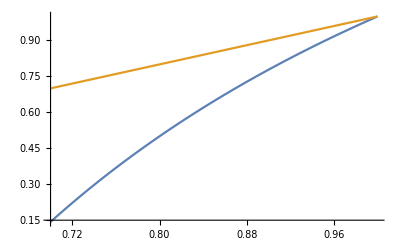

```mathematica
Plot[{Linf,L},{L,0.7,1}]
```

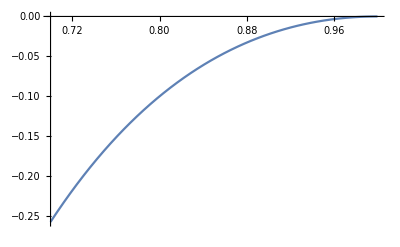

```mathematica
Plot[1- 2 *L +Linf,{L,0.7,1}]
```

### Solving Mean activity (L) as a function of ε

```mathematica
SL=L /. Solve[(1-L) (1-Linf)/ (L^2) == eps,L]
```

{2/(3 eps)+(-4+12 eps)/(3 eps (-8+36 eps-27 eps^2+3 √3 √(-8 eps^3+27 eps^4))^(1/3))-((-8+36 eps-27 eps^2+3 √3 √(-8 eps^3+27 eps^4))^(1/3))/(3 eps),2/(3 eps)-((1+ⅈ √3) (-4+12 eps))/(6 eps (-8+36 eps-27 eps^2+3 √3 √(-8 eps^3+27 eps^4))^(1/3))+((1-ⅈ √3) (-8+36 eps-27 eps^2+3 √3 √(-8 eps^3+27 eps^4))^(1/3))/(6 eps),2/(3 eps)-((1-ⅈ √3) (-4+12 eps))/(6 eps (-8+36 eps-27 eps^2+3 √3 √(-8 eps^3+27 eps^4))^(1/3))+((1+ⅈ √3) (-8+36 eps-27 eps^2+3 √3 √(-8 eps^3+27 eps^4))^(1/3))/(6 eps)}

```mathematica
L= First[SL]
```

2/(3 eps)+(-4+12 eps)/(3 eps (-8+36 eps-27 eps^2+3 √3 √(-8 eps^3+27 eps^4))^(1/3))-((-8+36 eps-27 eps^2+3 √3 √(-8 eps^3+27 eps^4))^(1/3))/(3 eps)

```mathematica
Series[L,{eps,0,2}]
```

L

### PRDM9 diversity (Ke) as a function of ε

#### rho = Ne * v * r_0 * \alpha

```mathematica
K= FullSimplify[ rho * L /(1- 2 *L +Linf)]
```

-((48 (1-3 eps)^2 rho)/((8+3 √3 √(eps^3 (-8+27 eps))) (-8+9 (4-3 eps) eps+3 √3 √(eps^3 (-8+27 eps)))^(2/3)-16 (-2+(-8+9 (4-3 eps) eps+3 √3 √(eps^3 (-8+27 eps)))^(1/3))+9 eps^2 (32-16 (-8+9 (4-3 eps) eps+3 √3 √(eps^3 (-8+27 eps)))^(1/3)+3 (-8+9 (4-3 eps) eps+3 √3 √(eps^3 (-8+27 eps)))^(2/3))-12 eps (16-8 (-8+9 (4-3 eps) eps+3 √3 √(eps^3 (-8+27 eps)))^(1/3)+3 (-8+9 (4-3 eps) eps+3 √3 √(eps^3 (-8+27 eps)))^(2/3))))

### First order approximation of Ke

```mathematica
FullSimplify[Series[K,{eps,0,1}]]
```

-rho/eps-rho/(√2 √eps)+rho/4-(5 rho √eps)/(16 √2)+(rho eps)/4+O[eps]^(3/2)

## Third order approximation

```mathematica
ClearAll["Global`*"]
```

### Third order approximation of Mimimun activity (Linf) as a function of L

```mathematica
SX = x /.Solve[L(x-x^2/2+x^3/3)==x, x]
```

{0,(3 L-√3 √(16 L-13 L^2))/(4 L),(3 L+√3 √(16 L-13 L^2))/(4 L)}

```mathematica
Linf= FullSimplify[1+SX[[2]]]
```

7/4-(√(48-39 L))/(4 √L)

```mathematica
FullSimplify[1- 2 *L +Linf]
```

11/4-(√(48-39 L))/(4 √L)-2 L

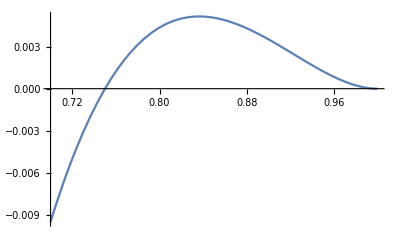

```mathematica
Plot[1- 2 *L +Linf,{L,0.7,1}]
```

### Solving mean activity (L) as a function of ε

```mathematica
Solve[(1-L) (1-Linf)/ (L^2) == eps,L]
```

{{L→Root[-6+18 #1-18 #1^2+(6+3 eps) #1^3-3 eps #1^4+2 eps^2 #1^5&,1]},{L→Root[-6+18 #1-18 #1^2+(6+3 eps) #1^3-3 eps #1^4+2 eps^2 #1^5&,2]},{L→Root[-6+18 #1-18 #1^2+(6+3 eps) #1^3-3 eps #1^4+2 eps^2 #1^5&,3]},{L→Root[-6+18 #1-18 #1^2+(6+3 eps) #1^3-3 eps #1^4+2 eps^2 #1^5&,4]},{L→Root[-6+18 #1-18 #1^2+(6+3 eps) #1^3-3 eps #1^4+2 eps^2 #1^5&,5]}}

### Approximation of mean activity (L) as a function of ε

```mathematica
serie= Series[(1-L) (1-Linf)/ (L^2),{L,1,3}]
```

2 (L-1)^2-10/3 (L-1)^3+O[L-1]^4

```mathematica
SL = L/. Solve[Normal[serie ]== eps,L]
```

{1/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3)),6/5+(1+ⅈ √3)/(5 2^(1/3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))+((1-ⅈ √3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/(10 2^(2/3)),6/5+(1-ⅈ √3)/(5 2^(1/3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))+((1+ⅈ √3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/(10 2^(2/3))}

```mathematica
L= SL[[1]]
```

1/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))

```mathematica
FullSimplify[1-L]
```

1/10 (-2+(2 2^(2/3))/(-4+75 eps+5 √3 √(eps (-8+75 eps)))^(1/3)+(-8+150 eps+10 √3 √(eps (-8+75 eps)))^(1/3))

### PRDM9 diversity (Ke) as a function of ε

#### rho = Ne * v * r_ 0 * \alpha

```mathematica
K = rho * L /(1- 2 *L +Linf)
```

((6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3)) rho)/(5 (11/4-2/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))-(√5 √(48-39/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))))/(4 √(6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3)))))

```mathematica
FullSimplify[Series[K,{eps,0,2}]]
```

(3 rho)/eps+(19 rho)/(√2 √eps)+(295 rho)/12+(12887 rho √eps)/(144 √2)+(2527 rho eps)/18+(21219061 rho eps^(3/2))/(41472 √2)+(1006033 rho eps^2)/1296+O[eps]^(5/2)